```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
```

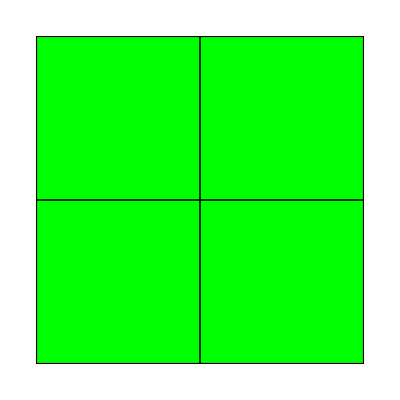

```mathematica
(*Uvozimo elemente ter node*)
Elements = Import["Data4ele/elements4.txt","Table","FieldSeparators"->","];
Nodes = Import["Data4ele/nodes4.txt","Table","FieldSeparators"->","];
Nodes = Drop[Nodes, None, {1}];(*odstrani prvi stolpec*)
Elements = Drop[Elements, None, {1}];

(*Prikaz elementov*)
ELplot= Table[{
	Graphics[{Green,EdgeForm[Black],Polygon[Nodes[[Elements[[i]]]]]}]},
	{i,1,Length[Elements]}];
Show[ELplot]
```

Part::take: Cannot take positions 2 through 4 in {---------}.

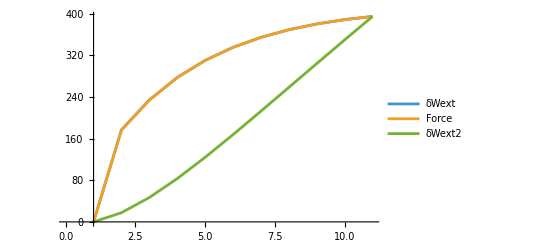

```mathematica
(*Uvoz podatkov -> Sila*)
Force = Import["Data4ele/Sila_4ele.txt", "Table", HeaderLines -> 3][[1;;-5,2]];
δWext = 1 * Force;
(*Pomiki ter napetosti*)
U = Import["Data4ele/Pomiki_4ele.txt", "Table", HeaderLines -> 3][[1;;-5, 2]];
Nap = Import["Data4ele/Napetost_4ele.txt", "Table", HeaderLines -> 4][[1;;-5, 2;;4]];
δWext2 = Force U;

ListLinePlot[{δWext, Force, δWext2}, AxesOrigin->{1,0}, PlotLegends->{"δWext","Force" ,"δWext2"}]
```

```mathematica
Nap // MatrixForm
```

(0. | 0. | 0.
194.265 | 3.37458×10^-15 | -0.00372638
280.809 | -1.56437×10^-15 | 0.035997
360.421 | -3.01007×10^-17 | 0.0564863
434.13 | 6.16342×10^-15 | 0.0636012
502.754 | -6.90929×10^-15 | 0.0659995
566.949 | 7.70401×10^-15 | 0.0660674
627.253 | 2.02589×10^-15 | 0.065018
684.111 | 6.82228×10^-14 | 0.0634646
737.895 | -6.96267×10^-14 | 0.061716
788.921 | 1.82939×10^-14 | 0.0599239)

```mathematica
(*Uvoz gradientov*)
(*FJSON[frame][element][Gauss Integration Point][Variable -> x,y,F]*)
(*F = FJSON[ToString[frame]][ToString[element]][ToString[integracijsaTocka]]["F"];*)
FJSON = Import["/Users/vid/Documents/FS-MAG/5. Magisterij/Projektni Praktikum/log2grad/Log2F/Grad_0_PHANTOM.json","RawJSON"];
```

```mathematica
(*Iteracija po framih*)
Frames = Length[Keys[FJSON]];
nelements = Length[Keys[FJSON[["1"]]]];
ngpoint = Length[Keys[FJSON[["1"]][[ToString[Keys[FJSON[["1"]]][[1]]]]]]];
Δt = 1/(Frames-1);

(*pred racunanjem dela izracunam Velocity gradient -> δv *)
δv = Table[{},{i,Frames}];
δv[[-1]] = {1,1,1,1,1}; (*zadnja vrstica -> je pravilno*)
iterableFrames = 10;
For[frame=0, frame < iterableFrames, frame++,
	For[nele = 1, nele <= nelements, nele++,
	For[ngp = 1, ngp <= ngpoint, ngp++,
		(*Print["Frame, ",frame+1," Integracijska tocka: ",ngp];*)
		Subscript[F, t] = FJSON[[ToString[frame]]][[ToString[nele]]][[ToString[ngp]]][["F"]] ;
		Subscript[F, t+1]= FJSON[[ToString[frame+1]]][[ToString[nele]]][[ToString[ngp]]][["F"]];
              (*Print["F_t: ",Subscript[F, t]];
		Print["F_(t + 1): ",Subscript[F, t+1]];
		Print[Subscript[F, t+1] - Subscript[F, t]];*)
		δv[[frame+1]] = 1/Δt (Subscript[F, t+1] - Subscript[F, t]);
]; (*gp*)
]; (*element*)
];(*frame*)
```

```mathematica
δWint = {}; (*Notranje virtualno delo za vse frame*)
(*Jacobian matrix*)
(*Mapping the determinant*)


For[frame = 1, frame <= Frames, frame ++,
det = {};
Subscript[𝒯, 1] := {Subscript[𝓍, 1],Subscript[𝓎, 1]} = {-1,-1};
Subscript[𝒯, 2] := {Subscript[𝓍, 1],Subscript[𝓎, 1]} = {1,-1};
Subscript[𝒯, 3] := {Subscript[𝓍, 1],Subscript[𝓎, 1]} = {1,1};
Subscript[𝒯, 4] := {Subscript[𝓍, 1],Subscript[𝓎, 1]} = {-1,1};
Subscript[ψ, i_][𝒳_, 𝒴_] := 1/4(1 + Subscript[𝒯, i][[1]] * 𝒳) *(1 + Subscript[𝒯, i][[2]]  * 𝒴);


For[j =1, j <= Length[Elements], j++,
	x = Nodes[[Elements[[j]]]][[;;,1]];
	y = Nodes[[Elements[[j]]]][[;;,2]];

	X[𝒳_, 𝒴_]  := Sum[Subscript[ψ, i][𝒳, 𝒴] x[[i]],{i,1,4}];
	Y[𝒳_, 𝒴_]  := Sum[Subscript[ψ, i][𝒳, 𝒴] y[[i]],{i,1,4}];
	J[𝒳_, 𝒴_]  = ({{D[X[𝒳, 𝒴], 𝒳], D[Y[𝒳, 𝒴], 𝒳]}, {D[X[𝒳, 𝒴], 𝒴], D[Y[𝒳, 𝒴], 𝒴]}});
	(*J[𝒳_, 𝒴_] = ({{D[X[𝒳, 𝒴],𝒳], D[Y[𝒳, 𝒴],𝒳]}, {D[X[𝒳, 𝒴],𝒴], D[Y[𝒳, 𝒴],𝒴]}});*)
];
det = Append[det,
{
Det[J[-1/(√3),-1/(√3)]],
Det[J[1/(√3),-1/(√3)]],
Det[J[-1/(√3),1/(√3)]],
Det[J[1/(√3),1/(√3)]]
}
];

(*
1. For -> index ele -> elementi
	2. For -> index gp -> integrac. tocka
*)
Fframe = FJSON[ ToString[frame-1]];

For[ele=1, ele <= Length[Elements], ele++,
Fele = Fframe[ ToString[ele]];
δWinte = 0;
For[gp = 1, gp <= 4, gp++,
	F = Fele[ ToString[gp]]["F"];
	F11 = F[[1]];
	F12 = F[[2]];
	F21 = F[[3]];
	F22 = F[[4]];
	F33 = F[[5]];
	(*Napetosti*)
	σ11 = Nap[[frame,1]]; (*Prvi stolpec*)
	σ12 = Nap[[frame,2]]; (*Drugi stolpec*)
	σ22 = Nap[[frame,3]] ; 
	
	(*δv -> Ḟ*)
	δvf = δv[[frame]];
	δv11 = δvf[[1]];
	δv12 = δvf[[2]];
	δv21 = δvf[[3]];
	δv22 = δvf[[4]];
	δv33 = δvf[[5]];

			
	(*1. Piola-Kirchoff Stress -> p*)
	p11 = F33 (F22 σ11 - F12 σ12);
	p12 = - F21 F33 σ11 + F11 F33 σ12;
	p21 = F33 (F22 σ12 - F12 σ22);
	p22 = -F21 F22 σ12 + F11 F33 σ22;
			

	(*Print[δWinti]*)
	δW = (p11 δv11 + p12 δv12 + p21 δv21 + p22 δv22) *det[[1,gp]];
	δWinte += δW; (*Sum dela vseh gaussovih tock*)
];

(*
	To ni pravilno -> Potrebujemo gradient histrosi (velocity gradient);
*)
	δWint = Append[δWint, δWinte];
]

];
```

```mathematica
δWint
```

{0.,176.606,233.993,277.226,310.071,335.148,354.323,368.954,380.045,388.35,394.545}

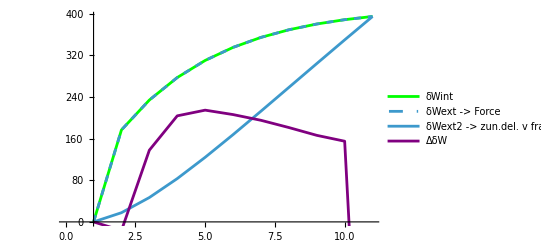

```mathematica
ListLinePlot[{δWext, δWext2, δWint},AxesOrigin->{1,0}, PlotLegends->{"δWext","δWext2","δWint"}, PlotStyle->{Dashed, Dashed, Red}];

P1 = ListLinePlot[{δWext},AxesOrigin->{1,0}, PlotLegends->{"δWext -> Force"}, PlotStyle->Dashed];
P2 = ListLinePlot[{ δWext2},AxesOrigin->{1,0}, PlotLegends->{"δWext2 -> zun.del. v frame"}, PlotStyle->{Normal, Blue}];
P3 = ListLinePlot[{ δWint},AxesOrigin->{1,0}, PlotLegends->{"δWint"}, PlotStyle->Green];
P4 = ListLinePlot[{ 10000(δWext - δWint)},AxesOrigin->{1,0}, PlotLegends->{"ΔδW"}, PlotStyle->Purple];

Show[P3, P1,P2,P4]
```

```mathematica
{Nap // MatrixForm , U// MatrixForm ,Force // MatrixForm}
```

{(0. | 0. | 0.
194.265 | 3.37458×10^-15 | -0.00372638
280.809 | -1.56437×10^-15 | 0.035997
360.421 | -3.01007×10^-17 | 0.0564863
434.13 | 6.16342×10^-15 | 0.0636012
502.754 | -6.90929×10^-15 | 0.0659995
566.949 | 7.70401×10^-15 | 0.0660674
627.253 | 2.02589×10^-15 | 0.065018
684.111 | 6.82228×10^-14 | 0.0634646
737.895 | -6.96267×10^-14 | 0.061716
788.921 | 1.82939×10^-14 | 0.0599239),(0.
0.1
0.2
0.3
0.4
0.5
0.6
0.7
0.8
0.9
1.),(0.
176.604
234.007
277.247
310.093
335.169
354.343
368.972
380.061
388.366
394.46)}

```mathematica
{Length[Force],Length[U],Length[Nap],Length[δv]}
```

{11,11,11,11}

```mathematica
Keys[FJSON]
```

{0,1,2,3,4,5,6,7,8,9,10}

```mathematica
{δWext,δWext2, δWint}
```

{{0.,176.604,234.007,277.247,310.093,335.169,354.343,368.972,380.061,388.366,394.46},{0.,17.6604,46.8014,83.174,124.037,167.585,212.606,258.281,304.049,349.529,394.46},{0.,176.606,233.993,277.226,310.071,335.148,354.323,368.954,380.045,388.35,394.545}}

```mathematica
δWext -  δWint
```

{0.,-0.00166576,0.0137727,0.0203688,0.0214602,0.0206113,0.0195119,0.0181216,0.0166229,0.0154944,-0.084745}

```mathematica
δWint / δWext
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

{Indeterminate,1.00001,0.999941,0.999927,0.999931,0.999939,0.999945,0.999951,0.999956,0.99996,1.00021}